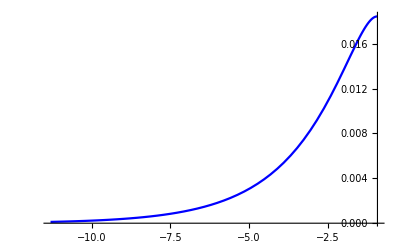

```mathematica
J=3;
Z1=1;
Z2=3;
Δ=√2;
μ=-1;
μN=10;
EE1=Δ*(μ-Δ^2/4)^(1/2);
S=1/2;
m1=-1/2;
n1=-3/2;
F2=Sqrt[(S-m1)*(S+m1+1)];
F4=Sqrt[(S-n1)*(S+n1+1)];
η=1;
ξ=2/Δ;
L=13/10*ξ;
EE1=Δ*(μ-Δ^2/4)^(1/2);
EE2=Abs[μ];
ϕ=Pi/5;
n=0.000001*0;
η=1;
ξ=2/Δ;
kI1=I*((Δ^2/2-μ)+(n^2-EE1^2)^(1/2))^(1/2);
kI2=-I*((Δ^2/2-μ)-(n^2-EE1^2)^(1/2))^(1/2);
kC1=((μ-Δ^2/2)+I*(EE1^2-n^2)^(1/2))^(1/2);
kC2=((μ-Δ^2/2)-I*(EE1^2-n^2)^(1/2))^(1/2);
ke=(μN)^(1/2)*(1+n/μN)^(1/2);
kh=(μN)^(1/2)*(1-n/μN)^(1/2);
qe=kI1;
qh=kI2;
γe=(n+qe^2-μ)/(Δ*qe);
γh=(n+qh^2-μ)/(Δ*qh);
γγe=-γe;
γγh=-γh;
Clear[α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44];
x1=0;
G[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(2*qe*γe+Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*γh+Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2)), 0, -2ke, 2ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, (2*qe*γe+Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*γh+Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, -2ke, 2ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, (-2*qe+Δ*γe-2*I*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh-Δ*γh-2*I*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 0, 2kh, -2kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(-2*qe+Δ*γe-2*I*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh-Δ*γh-2*I*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 2kh, -2kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0}, {0, 0, 0, 0, (2*ke+I*J*m1)*Exp[I*ke*L/2], (-2*ke+I*J*m1), I*J*F2*Exp[I*ke*L/2], I*J*F2, 0, 0, 0, 0, -2*ke, 2*ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, I*J*F2*Exp[I*ke*L/2], I*J*F2, (2*ke-I*J*(m1+1))*Exp[I*ke*L/2], -(2ke+I*J*(m1+1)), 0, 0, 0, 0, 0, 0, -2ke, 2*ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, I*J*F2*Exp[-I*kh*L/2], I*J*F2, -(2*kh+I*J*(m1+1))*Exp[-I*kh*L/2], (2*kh-I*J*(m1+1)), 0, 0, 0, 0, 0, 0, 2*kh, -2*kh*Exp[-I*kh*L/2], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (-2*kh+I*J*m1)*Exp[-I*kh*L/2], (2*kh+I*J*m1), I*J*F2*Exp[-I*kh*L/2], I*J*F2, 0, 0, 0, 0, 2*kh, -2*kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh*Exp[I*ϕ]/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh*Exp[I*ϕ]/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (2*ke-2*I*Z2)*Exp[I*ke*L/2], -(2*ke+2*I*Z2), 0, 0, Δ*(-Exp[I*ϕ])*Exp[-I*kh*L/2], Δ*(-Exp[I*ϕ]), 0, 0, -(2*qe*γe*Exp[I*ϕ])/((1+Abs[γe]^2)^(1/2)), 0, -(2*qh*γh*Exp[I*ϕ])/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (2*ke-2*I*Z2)*Exp[I*ke*L/2], -(2*ke+2*I*Z2), 0, 0, Δ*(-Exp[I*ϕ])*Exp[-I*kh*L/2], Δ*(-Exp[I*ϕ]), 0, -(2*qe*γe*Exp[I*ϕ])/((1+Abs[γe]^2)^(1/2)), 0, -(2*qh*γh*Exp[I*ϕ])/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Δ*(Exp[-I*ϕ])*Exp[I*ke*L/2], Δ*(Exp[-I*ϕ]), 0, 0, -(2*kh+2*I*Z2)*Exp[-I*kh*L/2], (2*kh-2*I*Z2), 0, -(2*qe*1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*1)/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Δ*(Exp[-I*ϕ])*Exp[I*ke*L/2], Δ*(Exp[-I*ϕ]), 0, 0, -(2*kh+2*I*Z2)*Exp[-I*kh*L/2], (2*kh-2*I*Z2), 0, 0, -(2*qe)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh)/((1+Abs[γh]^2)^(1/2)), 0}});
GN[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, -γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(2*qe*γe+Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*γh+Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2)), 0, -2ke, 2ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, (2*qe*γe+Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*γh+Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, -2ke, 2ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, (-2*qe+Δ*γe-2*I*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh-Δ*γh-2*I*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 0, 2kh, -2kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {(-2*qe+Δ*γe-2*I*Z1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh-Δ*γh-2*I*Z1)/((1+Abs[γh]^2)^(1/2)), 0, 0, 0, 0, 0, 2kh, -2kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, 0, 0, 0, 0, -1, -Exp[-I*kh*L/2], 0, 0, 0, 0}, {0, 0, 0, 0, (2*ke+I*J*n1)*Exp[I*ke*L/2], (-2*ke+I*J*n1), I*J*F4*Exp[I*ke*L/2], I*J*F4, 0, 0, 0, 0, -2*ke, 2*ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, I*J*F4*Exp[I*ke*L/2], I*J*F4, (2*ke-I*J*(n1+1))*Exp[I*ke*L/2], -(2ke+I*J*(n1+1)), 0, 0, 0, 0, 0, 0, -2ke, 2*ke*Exp[I*ke*L/2], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, I*J*F4*Exp[-I*kh*L/2], I*J*F4, -(2*kh+I*J*(n1+1))*Exp[-I*kh*L/2], (2*kh-I*J*(n1+1)), 0, 0, 0, 0, 0, 0, 2*kh, -2*kh*Exp[-I*kh*L/2], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (-2*kh+I*J*n1)*Exp[-I*kh*L/2], (2*kh+I*J*n1), I*J*F4*Exp[-I*kh*L/2], I*J*F4, 0, 0, 0, 0, 2*kh, -2*kh*Exp[-I*kh*L/2], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh*Exp[I*ϕ]/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[I*ke*L/2], 1, 0, 0, 0, 0, 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh*Exp[I*ϕ]/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Exp[-I*kh*L/2], 1, 0, 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (2*ke-2*I*Z2)*Exp[I*ke*L/2], -(2*ke+2*I*Z2), 0, 0, Δ*(-Exp[I*ϕ])*Exp[-I*kh*L/2], Δ*(-Exp[I*ϕ]), 0, 0, -(2*qe*γe*Exp[I*ϕ])/((1+Abs[γe]^2)^(1/2)), 0, -(2*qh*γh*Exp[I*ϕ])/((1+Abs[γh]^2)^(1/2)), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (2*ke-2*I*Z2)*Exp[I*ke*L/2], -(2*ke+2*I*Z2), 0, 0, Δ*(-Exp[I*ϕ])*Exp[-I*kh*L/2], Δ*(-Exp[I*ϕ]), 0, -(2*qe*γe*Exp[I*ϕ])/((1+Abs[γe]^2)^(1/2)), 0, -(2*qh*γh*Exp[I*ϕ])/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Δ*(Exp[-I*ϕ])*Exp[I*ke*L/2], Δ*(Exp[-I*ϕ]), 0, 0, -(2*kh+2*I*Z2)*Exp[-I*kh*L/2], (2*kh-2*I*Z2), 0, -(2*qe*1)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh*1)/((1+Abs[γh]^2)^(1/2))}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, Δ*(Exp[-I*ϕ])*Exp[I*ke*L/2], Δ*(Exp[-I*ϕ]), 0, 0, -(2*kh+2*I*Z2)*Exp[-I*kh*L/2], (2*kh-2*I*Z2), 0, 0, -(2*qe)/((1+Abs[γe]^2)^(1/2)), 0, (2*qh)/((1+Abs[γh]^2)^(1/2)), 0}});
H[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2))}, {0}, {0}, {-1/((1+Abs[γe]^2)^(1/2))}, {(-2*qe*γe-Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2))}, {0}, {0}, {(-2*qe+Δ*γe+2*I*Z1)/((1+Abs[γe]^2)^(1/2))}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H1[ϕ_]:=({{0}, {-γe/((1+Abs[γe]^2)^(1/2))}, {-1/((1+Abs[γe]^2)^(1/2))}, {0}, {0}, {(-2*qe*γe-Δ+2*I*γe*Z1)/((1+Abs[γe]^2)^(1/2))}, {(-2*qe+Δ*γe+2*I*Z1)/((1+Abs[γe]^2)^(1/2))}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H2[ϕ_]:=({{γh/((1+Abs[γh]^2)^(1/2))}, {0}, {0}, {-1/((1+Abs[γh]^2)^(1/2))}, {(-2*qh*γh-Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2))}, {0}, {0}, {(2*qh-Δ*γh+2*I*Z1)/((1+Abs[γh]^2)^(1/2))}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
H3[ϕ_]:=({{0}, {γh/((1+Abs[γh]^2)^(1/2))}, {-1/((1+Abs[γh]^2)^(1/2))}, {0}, {0}, {(-2*qh*γh-Δ-2*I*γh*Z1)/((1+Abs[γh]^2)^(1/2))}, {(2*qh-Δ*γh+2*I*Z1)/((1+Abs[γh]^2)^(1/2))}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}});
Sol[ϕ_]:=LinearSolve[G[ϕ],H[ϕ]];
Sol1[ϕ_]:=LinearSolve[GN[ϕ],H1[ϕ]];
Sol2[ϕ_]:=LinearSolve[G[ϕ],H2[ϕ]];
Sol3[ϕ_]:=LinearSolve[GN[ϕ],H3[ϕ]];
b11=Sol[ϕ][[1,1]];
b12=Sol[ϕ][[2,1]];
a11=Sol[ϕ][[3,1]];
a12=Sol[ϕ][[4,1]];
b21=Sol1[ϕ][[1,1]];
b22=Sol1[ϕ][[2,1]];
a21=Sol1[ϕ][[3,1]];
a22=Sol1[ϕ][[4,1]];
b31=Sol2[ϕ][[1,1]];
b32=Sol2[ϕ][[2,1]];
a31=Sol2[ϕ][[3,1]];
a32=Sol2[ϕ][[4,1]];
b41=Sol3[ϕ][[1,1]];
b42=Sol3[ϕ][[2,1]];
a41=Sol3[ϕ][[3,1]];
a42=Sol3[ϕ][[4,1]];
fuuOS=1/8 ⅈ η (1/(qh γe-qe γh)((b42+b31) ⅇ^(-ⅈ qe (x+L/2)+ⅈ qh (x1+L/2)) γe^2+γh (+(b11+b22) ⅇ^(-ⅈ qe (x+x1+L)) γe-(a42+a31) ⅇ^(ⅈ qh (x+x1+L)) γe-(a22+a11) ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) γh))+1/(qe γe-qh γh)(+(b11+b22) ⅇ^(-ⅈ qe (x+x1+L))-(a42+a31) ⅇ^(ⅈ qh (x+x1+L))-ⅇ^(-ⅈ qe (x+L/2)+ⅈ qh (x1+L/2)) (Conjugate[a22]+Conjugate[a11])+ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) (Conjugate[b42]+Conjugate[b31])));
fuuES=1/8 ⅈ η (((b42+b31) ⅇ^(-ⅈ qe (x+L/2)+ⅈ qh (x1+L/2)) γe^2+γh (-(a22+a11) ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) γh))/(qh γe-qe γh)-1/(qe γe-qh γh)(-ⅇ^(-ⅈ qe(x+L/2)+ⅈ qh (x1+L/2)) (Conjugate[a22]+Conjugate[a11])+ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) (Conjugate[b42]+Conjugate[b31])));
f3OS=1/8 ⅈ ⅇ^(-ⅈ qe (x+x1+L)) η (((b41+b32) ⅇ^(ⅈ (qe+qh) (x1+L/2)) γe^2-γh (-(b12+b21) γe+(a41+a32) ⅇ^(ⅈ (qe+qh) (x+x1+L)) γe+(a21+a12) ⅇ^(ⅈ (qe+qh) (x+L/2)) γh))/(qh γe-qe γh)+1/(qe γe-qh γh)((b12+b21)-(a41+a32) ⅇ^(ⅈ (qe+qh) (x+x1+L))-ⅇ^(ⅈ (qe+qh) (x1+L/2)) (Conjugate[a12]+Conjugate[a21])+ⅇ^(ⅈ (qe+qh) (x+L/2))(Conjugate[b41]+Conjugate[b32])));
f3ES=(ⅈ η (-(a21+a12) ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) γh^2+(b41+b32) ⅇ^(-ⅈ qe (x+L/2)+ⅈ qh (x1+L/2)) γe^2))/(8 (qh γe-qe γh))-1/(8(qe γe-qh γh))ⅈ η (-ⅇ^(ⅈ (-qe (x+L/2)+qh (x1+L/2))) (Conjugate[a12]+Conjugate[a21])+ⅇ^(ⅈ (qh (x+L/2)-qe (x1+L/2))) (Conjugate[b41]+Conjugate[b32]));
Plot[Abs[f3ES],{x,-L/2,-8*ξ},AxesOrigin->{-L/2,0},PlotRange->All,PlotStyle->Blue]
```